```mathematica
Data:={4.2,432,3.3,17,26,1.3,7.4,29.1,44,47,115,82,75,76,48,43,3.7,6.1,25.6,33,38,120,173,150,44,30,19,18,20,16,4.9,14.3,13.5,14.8,16.3,18,19.5,7.9,21.8,22.1,24.7,26.3,28.3,30.5,9.9,27.2,30,69,161,178,222,210,61,27,2.8,5.6,12,31,111,43}
```

```mathematica
Max[Data]-Min[Data]
```

430.7

```mathematica
catlength=Ceiling[(Max[Data]-Min[Data])/6]
```

72

```mathematica
n=6
```

6

```mathematica
categiories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{0.8,72.8,144.8,216.8,288.8,360.8,432.8}

```mathematica
Histogram[Data,{Min[categories]},Max[categiories],catlength},Ticks->{categories,Automatic}]
```

```mathematica
categories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{0.8,72.8,144.8,216.8,288.8,360.8,432.8}

```mathematica
Histogram[Data,{Min[categories]},Max[categiories],catlength},Ticks->{categories,Automatic}]
```

```mathematica
Histogram[Data,{Min[categories]},Max[categiories],catlength},Ticks->{categories,Automatic}]
```

Syntax::bktmcp: 表达式 "Histogram[Data,{Min[categories]},Max[categiories],catlength" 没有后面的 "]".

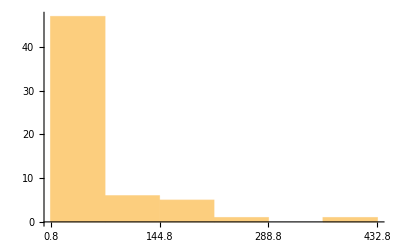

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```

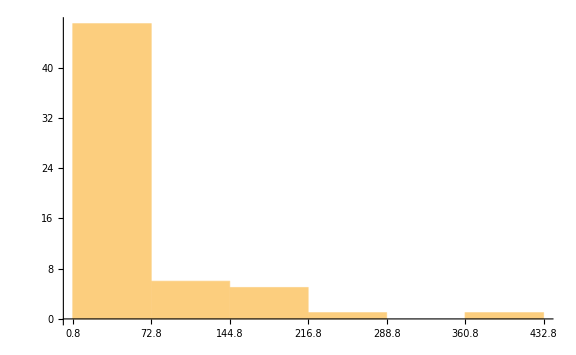

```mathematica
Show[%7,ImageSize->Large]
```

```mathematica
Show[%8,ImageSize->Full]
```

-Graphics-

```mathematica
Data:={4.2,432,3.3,17,26,1.3,7.4,29.1,44,47,115,82,75,76,48,43,3.7,6.1,25.6,33,38,120,173,150,44,30,19,18,20,16,4.9,14.3,13.5,14.8,16.3,18,19.5,7.9,21.8,22.1,24.7,26.3,28.3,30.5,9.9,27.2,30,69,161,178,222,210,61,27,2.8,5.6,12,31,111,43}*3.27868
```

```mathematica
Max[Data]-Min[Data]
```

1412.13

```mathematica
catlength=Ceiling[(Max[Data]-Min[Data])/6]
```

236

```mathematica
categiories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{3.76228,239.762,475.762,711.762,947.762,1183.76,1419.76}

```mathematica
categories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{3.76228,239.762,475.762,711.762,947.762,1183.76,1419.76}

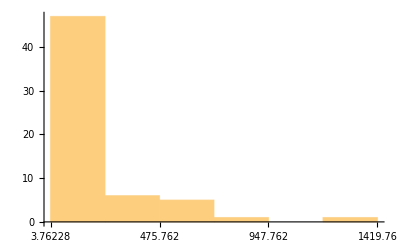

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```

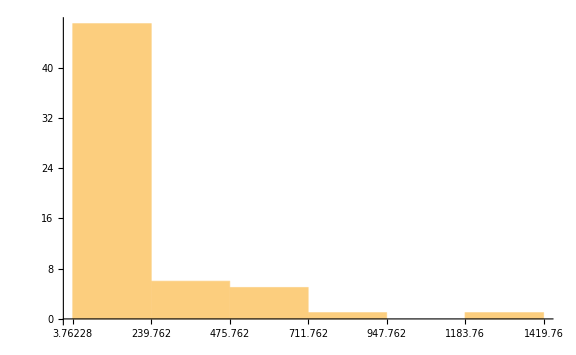

```mathematica
Show[%15,ImageSize->Large]
```

```mathematica
Data:={4,4,3,1,2,1,7,2,4,4,1,8,7,7,4,4,3,6,2,3,3,1,1,1,4,3,1,1,2,1,4,1,1,1,1,1,1,7,2,2,2,2,2,3,9,2,3,6,1,1,2,2,6,2,2,5,1,3,1,4}
```

```mathematica
Max[Data]-Min[Data]
```

8

```mathematica
catlength=Ceiling[(Max[Data]-Min[Data])/6]
```

2

```mathematica
categories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{0.5,2.5,4.5,6.5,8.5,10.5,12.5}

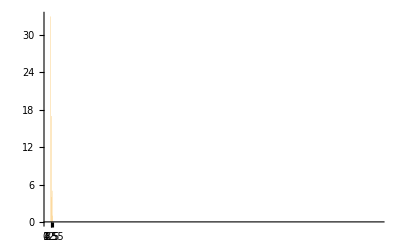

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```

```mathematica
Show[%21,ImageSize->Full]
```

-Graphics-

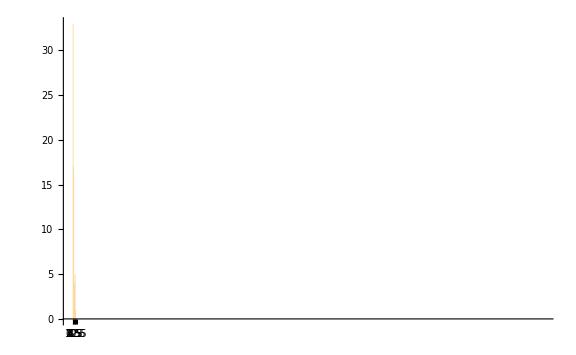

```mathematica
Show[%22,ImageSize->Large]
```

```mathematica
Show[%24,ImageSize->Full]
```

-Graphics-

```mathematica
Show[%22,ImageSize->Large]
```

-Graphics-

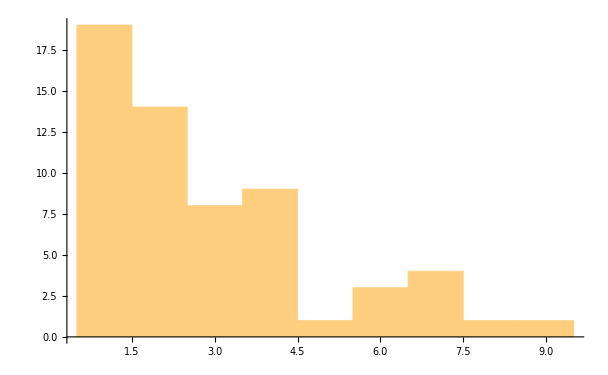

```mathematica
Histogram[Data]
```

```mathematica
Data:={4.2,432,3.3,17,26,1.3,7.4,29.1,44,47,115,82,75,76,48,43,3.7,6.1,25.6,33,38,120,173,150,44,30,19,18,20,16,4.9,14.3,13.5,14.8,16.3,18,19.5,7.9,21.8,22.1,24.7,26.3,28.3,30.5,9.9,27.2,30,69,161,178,222,210,61,27,2.8,5.6,12,31,111,43}*3.27868
```

```mathematica
Data
```

{13.7705,1416.39,10.8196,55.7376,85.2457,4.26228,24.2622,95.4096,144.262,154.098,377.048,268.852,245.901,249.18,157.377,140.983,12.1311,19.9999,83.9342,108.196,124.59,393.442,567.212,491.802,144.262,98.3604,62.2949,59.0162,65.5736,52.4589,16.0655,46.8851,44.2622,48.5245,53.4425,59.0162,63.9343,25.9016,71.4752,72.4588,80.9834,86.2293,92.7866,99.9997,32.4589,89.1801,98.3604,226.229,527.867,583.605,727.867,688.523,199.999,88.5244,9.1803,18.3606,39.3442,101.639,363.933,140.983}

```mathematica
Data:={1,1,1,5,8,4,2,9,1,1,3,2,2,2,1,1,1,1,8,1,1,3,5,4,1,9,6,5,6,5,1,4,4,4,5,5,6,2,7,7,8,8,9,9,3,8,9,2,5,5,7,6,1,8,9,1,3,1,3,1}
```

```mathematica
Max[Data]-Min[Data]
```

8

```mathematica
{1,1,1,5,8,4,2,9,1,1,3,2,2,2,1,1,1,1,8,1,1,3,5,4,1,9,6,5,6,5,1,4,4,4,5,5,6,2,7,7,8,8,9,9,3,8,9,2,5,5,7,6,1,8,9,1,3,1,3,1}
```

{1,1,1,5,8,4,2,9,1,1,3,2,2,2,1,1,1,1,8,1,1,3,5,4,1,9,6,5,6,5,1,4,4,4,5,5,6,2,7,7,8,8,9,9,3,8,9,2,5,5,7,6,1,8,9,1,3,1,3,1}

```mathematica
Max[Data]-Min[Data]
```

8

```mathematica
catlength=Ceiling[(Max[Data]-Min[Data])/6]
```

2

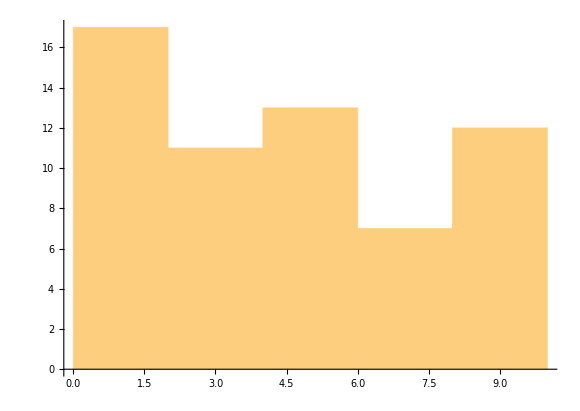

```mathematica
Histogram[Data]
```

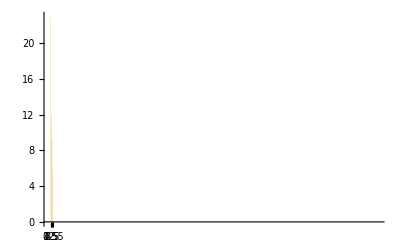

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```

```mathematica
catlength=Ceiling[(Max[Data]-Min[Data])/6]
```

2

```mathematica
categiories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{0.5,2.5,4.5,6.5,8.5,10.5,12.5}

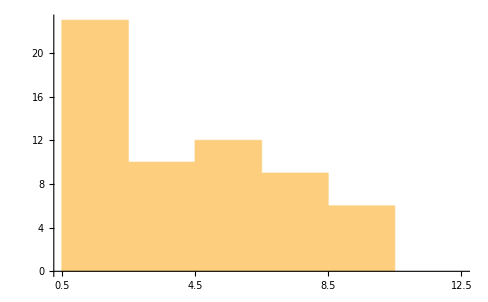

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```

```mathematica
Data:={4,4,3,1,2,1,7,2,4,4,1,8,7,7,4,4,3,6,2,3,3,1,1,1,4,3,1,1,2,1,4,1,1,1,1,1,1,7,2,2,2,2,2,3,9,2,3,6,1,1,2,2,6,2,2,5,1,3,1,4}
```

```mathematica
catlength=Ceiling[(Max[Data]-Min[Data])/6]
```

2

```mathematica
categiories=Table[Min[Data]-0.5+i catlength,{i,0,6}]
```

{0.5,2.5,4.5,6.5,8.5,10.5,12.5}

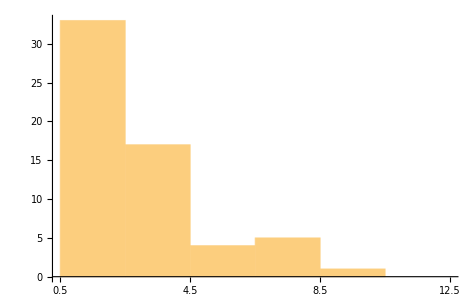

```mathematica
Histogram[Data,{Min[categories],Max[categiories],catlength},Ticks->{categories,Automatic}]
```